# Hyperdimensional Computing (HDC)

Brian Beckman

PRELIMINARY REVIEW DRAFT; NOT FOR CIRCULATION 
3 October 2023

## APU

How many bit-vectors of length 8192 can we store in the APU?

```mathematica
16 section/vr 24 vr/core 4 core/apu 4 eightKvecs/section
```

(6144 eightKvecs)/apu

## Glossary

```mathematica
{{BHV, Binary HyperVector}}
```

## BHV Object

Mathematica doesn’t have built-in Object-Oriented Programming, but it’s easy to simulate various aspects of it. Here, we bind a fixed set of function symbols — an interface — to instances of data-carrying Modules, instances that carry particular bit-vectors.

```mathematica
On[Assert];
ClearAll[asserte];
asserte[expected_,actual_]:=Assert[Echo[actual]===Echo@expected];
```

```mathematica
toHex[x_]:=
With[{cx=ToString[x]},
Which[
StringMatchQ[cx,RegularExpression["[a-f]"]],ToCharacterCode[cx][[1]]-87,
StringMatchQ[cx,RegularExpression["[A-F]"]],ToCharacterCode[cx][[1]]-55,
StringMatchQ[cx,RegularExpression["[0-9]"]],ToCharacterCode[cx][[1]]-48,
(*MatchQ[x,(a|b|c|d|e|f)],ToCharacterCode[ToString[x]][[1]]-87,
MatchQ[x,(A|B|C|D|E|F)],ToCharacterCode[ToString[x]][[1]]-48,
0<=x<=9,x,*)
True,Assert[False]]];
```

```mathematica
{Dynamic[toHex[x]],{SetterBar[Dynamic[x],{a,b,c,d,e,f,A,B,C,D,E,F,"a","b","c","d","e","f","A","B","C","D","E","F",0,1,2,3,4,5,6,7,8,9,"0","1","2","3","4","5","6","7","8","9","bang"},Appearance->"Vertical"->{Automatic,16}]}}
```

{,{ |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }}

```mathematica
(* declare (clear) the public interface symbols *)
ClearAll[bhv,
ones,zeros,copy,rands,nibs8,fromBin,fromHex,fromDimInt,(* factories *)
one,zero,rand,nib8,setBin,setHex,setInt,
setBit0,setBit1,flipBit0,flipBit1,flipFraction,(* setters *)
dim,prhex,ehex,prbin,ebin,asBin,asHex,asInt,(* getters, e is echof *)
onesComp,maj2,maj3,hmul,hsum,permute,(* operators *)
stdApart,related,unrelated,zScore,sigma,stdApart,(* statistical operators *)
noisy,distance,xor,and,or,not,erl,wrl,nock,comb,
hamming,sumGF2,prodGF2];(* GF(2) operators *)
(* implement the interface *)
bhv[bitDimIn:(_?IntegerQ):8192]:=
With[{PROBABILITY=0.5,NOMINALDISTANCE=0.5},
Module[{this,bitDimPR,integerPR},
Assert[Mod[bitDimIn,4]===0];
(* ******** private data; PR means private *)
bitDimPR=bitDimIn;
integerPR=0;
(* ******** factories *)
ones[dimx_Integer:8192]:=Module[{x=bhv[dimx]},one[x]];
zeros[dimx_Integer:8192]:=Module[{x=bhv[dimx]},zero[x]];
copy[this]:=fromDimInt[bitDimPR,integerPR];
rands[dimx_Integer:8192]:=Module[{x=bhv[dimx]},rand[x]];
nibs8[dimx_Integer:8192]:=Module[{},
fromHex[ConstantArray["8",Quotient[dimx,4]]]];
fromBin[bitx_List]:=Module[{that=bhv[0]},
setBin[that,bitx];that];
fromHex[hexes_List]:=Module[{that=bhv[0]},
setHex[that,hexes];that];
fromDimInt[dimx_Integer,int_Integer]:=Module[{that=bhv[dimx]},
setInt[that,int];that];
(* ******** class methods *)
Null;
(* ******** setters (side-effectors, mutators) *)
one[this]:=setBin[this,ConstantArray[1,bitDimPR]];
zero[this]:=setBin[this,ConstantArray[0,bitDimPR]];
rand[this]:=setBin[this,RandomInteger[{0,1},bitDimPR]];
nib8[this]:=nibs8[bitDimPR];
setBin[this,bitx_List]:=Module[{dimx=Length[bitx]},
Assert[AllTrue[bitx,((#===1)||(#===0))&]];
Assert[Mod[dimx,4]===0];
bitDimPR=dimx;integerPR=FromDigits[bitx,2];this];
setHex[this,hexes_List]:=Module[{
l=Length[hexes],
dits=toHex/@hexes},
(* Explicit Assert is too big. Something will go wrong in FromDigits if hexes is bogus. *)
bitDimPR=4l;integerPR=FromDigits[dits,16];this];
setInt[this,int_Integer]:=Module[{},
Assert[Length[IntegerDigits[int,2]]<=bitDimPR];
integerPR=int;this];
setBit1[this,idx1_Integer,val_Integer:1]:=Module[
{thatBits=asBin[this]},
Assert[val===1||val===0];
thatBits[[idx1]]=val;
fromBin[thatBits]];
setBit0[this,idx0_Integer,val_Integer:1]:=setBit1[this,idx0+1];
flipBit1[this,idx1_Integer]:=Module[
{thatBits=asBin[this]},
thatBits[[idx1]]=1-thatBits[[idx1]];
fromBin[thatBits]];
flipBit0[this,idx0_Integer]:=flipBit1[this,idx0+1];
flipFraction[this,p_Real]:=Module[
{thatBits=asBin[this],thoseBits},
thoseBits=Map[If[RandomReal[]>p,#,1-#]&,thatBits];
fromBin[thoseBits]];
(* ******** getters *)
dim[this]:=bitDimPR;
prhex[this]:=Print[MatrixForm[{asHex[this]}]];
ehex[this]:=(prhex[this];this);
prbin[this]:=Print[MatrixForm[{asBin[this]}]];
ebin[this]:=(prbin[this];this);
asBin[this]:=PadLeft[IntegerDigits[integerPR,2],bitDimPR];
asHex[this]:=PadLeft[IntegerDigits[integerPR,16],Quotient[bitDimPR, 4]]/.
{10->"A",11->"B",12->"C",13->"D",14->"E",15->"F"};
asInt[this]:=integerPR;
(* ******** operators *)
onesComp[this]:=fromBin[1-asBin[this]];
(* ******** statistical operators *)
noisy[this,probabilityOfFlip_Real?((0.0<=#<=1.0)&)]:=
Module[{that=bhv[0]},setBin[that,
Map[If[RandomReal[]<=probabilityOfFlip,1-#,#]&,asBin[this]]];
that];
sigma[this]:=Module[{p=PROBABILITY},√(bitDimPR p(1-p))];
stdApart[this,that_]:=(hamming[this,that]-bitDimPR/2)/sigma[this];
zScore[this]:=stdApart[this,rands[bitDimPR]];
related[this,that_,stds_Real:-6.]:=(stdApart[this,that]<stds);
unrelated[this,that_,stds_Real:-6.]:=(stdApart[this,that]>=stds);
distance[this,that_]:=hamming[this,that]*1.0/dim[this];
(* ******** Boolean & GF(2) operators *)
hamming[this,that_]:=HammingDistance[asBin[this],asBin[that]](* TODO OPTIMIZE! *);
hamming[this]:=Count[asBin[this],1];
xor[this,that_]:=sumGF2[this,that];
and[this,that_]:=prodGF2[this,that];
or[this,that_]:=fromDimInt[bitDimPR,BitOr[asInt[this],asInt[that]]];
not[this]:=onesComp[this];
erl[this]:=fromBin[RotateLeft[asBin[this]]];
wrl[this]:=fromBin[RotateRight[asBin[this]]];
comb[this,that_]:=not[xor[this,that]];
nock[this]:=
Module[{e,ee,eee,aaa},
e=erl@this;ee=erl@e;eee=erl@ee;
aaa=and[and[and[this,e],ee],eee];
and[nib8@this,aaa]];
sumGF2[this,that_]:=fromDimInt[bitDimPR,BitXor[asInt[this],asInt[that]]];
prodGF2[this,that_]:=fromDimInt[bitDimPR,BitAnd[asInt[this],asInt[that]]];
(* ******** operators *)
maj3[this, that_,theOther_]:=Module[{
x=asInt@this,
y=asInt@that,
z=asInt@theOther},
Assert[dim[this]===dim[that]===dim[theOther]];
fromDimInt[dim[this],BitOr[BitAnd[x,y],BitAnd[y,z],BitAnd[z,x]]]];
maj2[this,that_]:=maj3[this,that,rands[dim[this]]];
hmul[this,that_]:=(Assert[dim[this]===dim[that]];
fromDimInt[dim[this],BitXor[asInt@this,asInt@that]]);
hsum[this,those__]:=Module[{them={those},bins,h,rulz},
Assert[dim[this]===dim[#]]&/@them;
If[OddQ[Length[them]],AppendTo[them,rands[dim[this]]]];
bins=asBin/@Append[them,this];
rulz={
{{zs__}}/;And@@(#===0&/@{zs})->0,
{{os__}}/;And@@(#===1&/@{os})->1,
{{zs__},{os__}}/;Length[{zs}]>Length[{os}]->0,
{{zs__},{os__}}/;Length[{zs}]<Length[{os}]->1,
{xs___}:>(Print[{"xs",{xs}}];Echo@"bug")};
h=ReplaceAll[rulz]/@MapThread[SplitBy[Sort[{##}],Identity]&,bins];
fromBin[h]];
permute[this,p_?PermutationCyclesQ]:=fromBin[Permute[asBin@this,p]];
(* ******** value of this bhv constructor *)
this]];
bhv[]; (* symbols are not defined until bhv is called once *)
testDim=8192;
```

### Unit Tests

#### Permutations

```mathematica
PermutationCycles[{0,2,3,1}+1]
```

Cycles[{{2,3,4}}]

```mathematica
PermutationList[InversePermutation[PermutationCycles[{3,1,0,2}+1]]]-1
```

{2,1,3,0}

```mathematica
With[{d=32},
Module[{a=rands[d],p=RandomPermutation[d],pa,ipa},
Print[{"    p", p}];
Print[{"    a",asBin@a, asInt@a}];
pa=permute[a,p];
Print[{"  p.a",asBin@pa,asInt@pa}];ipa=permute[pa,InversePermutation[p]];
Print[{"i.p.a",asBin@ipa,asInt@ipa}];
Assert[asBin@ipa===asBin@a]
]]
```

{    p,Cycles[{{1,6,2,26,23,17,4,25,14,21,8,3,18,10,24,19,13,11,15,28,9,27,29},{5,12,22,7,16,20},{30,31}}]}

{    a,{1,1,1,1,1,0,0,1,0,1,0,0,1,1,0,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,0,1},4182564393}

{  p.a,{1,0,1,1,1,1,1,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,1,0,0,1,0,0,1},3211839945}

{i.p.a,{1,1,1,1,1,0,0,1,0,1,0,0,1,1,0,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,0,1},4182564393}

#### hsum

```mathematica
With[{d=32},
Module[{a=rands[d],b=rands[d],c=rands[d],m,h,q},
Print[{"a",asBin[a]}];
Print[{"b",asBin[b]}];
Print[{"c",asBin[c]}];
Print[{"m",m=asBin[maj3[a,b,c]]}];
Print[{"h",h=asBin[hsum[a,b,c] ]}];
Print[{"q",q=asBin[hsum@@{a,b,c}]}];
Assert[h===m===q]]]
```

{a,{1,0,0,0,1,0,0,1,1,1,0,0,1,1,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,1,1,0}}

{b,{1,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,1,1,0}}

{c,{1,1,0,1,0,1,1,0,0,1,1,0,1,1,0,1,0,0,0,1,1,0,1,0,0,0,0,1,0,0,1,0}}

{m,{1,0,0,1,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,1,1,0}}

{h,{1,0,0,1,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,1,1,0}}

{q,{1,0,0,1,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,1,1,0}}

### Smoke Tests

Check visually.

```mathematica
Module[{x=rands[16],y},
y=flipFraction[x,0.5];
Print[asHex[x]];
Print[asBin[x]];
Print[asBin[y]];
Print[hamming[x,y]];
Print[asBin@flipBit0[x,0]];
Print[asBin@x];]
```

{C,B,2,9}

{1,1,0,0,1,0,1,1,0,0,1,0,1,0,0,1}

{1,0,0,0,0,1,1,0,0,0,0,1,0,1,1,1}

9

{0,1,0,0,1,0,1,1,0,0,1,0,1,0,0,1}

{1,1,0,0,1,0,1,1,0,0,1,0,1,0,0,1}

## General Statistics

How many standards is a random bit-vector off from another random bit-vector?

```mathematica
zScore[rands[]]
```

-0.508233

Another way of testing the same thing:

```mathematica
stdApart[rands[],rands[]]
```

0.198874

The expected distance between two rands is half the bits:

```mathematica
distance[rands[],rands[]]
```

0.489014

Measure the standard deviation of the number of bits different between two rands — depends on the dimensionality, but not on the particular bit-data in the random, so is constant for a given dimensionality.

```mathematica
sigma[rands[]]
```

45.2548

The expected number of bits different between two random bit-vectors is half the dimension, with a standard deviation of √(dim*p(1-p), which is the Gaussian approximation of the Binomial distribution, practically accurate for the dimensions we consider in HDC. For a dimension of 8192 bits, that’s 4096±45.2548.

If some pair of vectors differ by fewer than this number, then it’s more likely that they are related. The likelihood is measured in negative sigmas: how many sigmas to the left of the mean are we? Adam’s library reckons -6 sigmas as the threshold for “related.”

From this blog by John D. Cook, we may translate between “nines” and “sigmas” to get decimal odds:

```mathematica
sigmasToNines[s_]:=(0.47+0.42Abs[s])^2;
ninesToSigmas[n_]:=2.37 √n-1.12;
```

Say we’re 6 sigmas off, that’s 8.94 nines, almost 1 in a billion chance that two vectors looked related without actually being related.

## Statistics of flipFraction

```mathematica
ClearAll[sample];
sample[size_Integer,pFrac_Real,dim_Integer:testDim]:=
Module[{origs=Table[rands[dim],{i,size}],mods,dists},
mods=flipFraction[#,pFrac]&/@origs;
dists=MapThread[hamming,{origs,mods}];
Print[<|"μ Hamming"->N@Mean[dists],"p"->pFrac,"pd"->pFrac dim,"σ"->N@StandardDeviation[dists],"√(p (1 - p) d)"->√(pFrac(1-pFrac) dim)|>];
dists];

(*AbsoluteTiming@sample[100,0.20,8192]*)
(* TEN MINUTES *)
ClearAll[timedData];
timedData=AbsoluteTiming@Table[sample[400,p,8192],{p,{0.10,0.20,0.30,0.40,0.50}}];
Short/@timedData
```

<|μ Hamming→819.14,p→0.1,pd→819.2,σ→26.9368,√(p (1 - p) d)→27.1529|>

<|μ Hamming→1638.59,p→0.2,pd→1638.4,σ→35.9376,√(p (1 - p) d)→36.2039|>

<|μ Hamming→2460.32,p→0.3,pd→2457.6,σ→41.2261,√(p (1 - p) d)→41.4767|>

<|μ Hamming→3276.44,p→0.4,pd→3276.8,σ→45.7861,√(p (1 - p) d)→44.3405|>

<|μ Hamming→4094.41,p→0.5,pd→4096.,σ→44.4967,√(p (1 - p) d)→45.2548|>

{59.9457,{«1»}}

```mathematica
ClearAll[cef];
cef[{{xmin_,xmax_},{ymin_,ymax_},{zmin_,zmax_}},___]:=Polygon[{{xmin,ymin,zmin},{xmax,ymin,zmin},{xmax,ymin,zmax},{xmin,ymin,zmax}}]
Module[{f},f[data_]:=Histogram3D[
MapIndexed[Thread[{#,#2[[1]]}]&,data],
{{-5000,5000,10},{1}},
BoxRatios->1,Axes->True,FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},
ChartElementFunction->cef];
GraphicsRow[{f[timedData[[2]]],f[timedData[[2]]-Mean/@timedData[[2]]]}]]
```

-Graphics-

```mathematica
ClearAll[skd];
skd=SmoothKernelDistribution[#]&/@(timedData[[2]]-Mean/@timedData[[2]]);
ListPointPlot3D[Table[{10 (#-1),x,PDF[skd[[#]],x]},
{x,-100,100,1}]&/@{1,2,3,4,5},Filling->Axis,BoxRatios->{1,1,1}]
```

-Graphics3D-

## Examples from Kanerva via pyBHV

> Assume that two meaningful vectors A and B are only 2500 bits apart— only 1/4 of their bits differ. The probability of this happening by chance is about zero, but a system can create such vectors when their meanings are related. Assume that 1/3 of the bits of A are changed at random; will the resulting “noisy” A' vector be closer to B than to A — would A' be falsely identified with B? It is possible but most unlikely because A' would be 4166 bits 10^4(d+e-2d e) away from B, on average, and only 3333 bits from A; the difference is 17 STDs. The (relative) distance from A' to B is d = e - 2d e with d = 1/4 and e = 1/3. Thus, adding e amount of noise to A increases the distance to B by (e - 2d e) on the average. Intuitively, most directions away from A in hyperspace are also away from B.

```mathematica
10^4(d+e-2d e)/.{d->0.25,e->1./3}
```

4166.67

```mathematica
BA$=Module[{A,B,Aprime,AB,AAprime,BAprime},
A=rands[];B=flipFraction[A,0.25];
Aprime=flipFraction[A,1./3.];
AB=distance[A,B];
AAprime=distance[A,Aprime];
BAprime=distance[B,Aprime];
Print[<|"AB"->AB,"AA'"->AAprime,"BA'"->BAprime|>];
BAprime];
```

<|AB→0.24707,AA'→0.330688,BA'→0.414429|>

```mathematica
Module[{e=1./3.,d=0.25},<|"d+e-2de"->d+e-2d e,"BA'"->BA$,"BA'/(d + e - 2  de)"->BA$/(d+e-2d e)|>]
```

<|d+e-2de→0.416667,BA'→0.414429,BA'/(d + e - 2  de)→0.994629|>

```mathematica
Solve[dp==d+e-2d e,{e}]
```

{{e→(d-dp)/(-1+2 d)}}

## N-Majority

Defined only for N=2M+1 odd. For even cases, add a uniformly random tiebreaker to make the collection of odd cardinality.

The ternary case has been covered. hsum is a brute-force computation. Unit test:

```mathematica
Module[{a=rands[],b=rands[],c=rands[]},
asInt@maj3[a,b,c]===asInt@hsum[a,b,c]]
```

True

Let N = 2M+1. N-Majority is True if all subsets of size M+1 for M even or size M for M odd are True. The number of such subsets is

```mathematica
subsetCount[M_]:=Piecewise[{{((2M+1)!)/((2M+1-(M+1))!(M+1)!), OddQ[M]}, {((2M+1)!)/((2M+1-M)!(M!)), EvenQ[M]}}]
```

A collection of 15 vectors has M = 7; 6435 cases to consider, too many to code up.

### Counterexample: N-Majority is not recursive 3-Majority

Recursive 3-Majority

```mathematica
ClearAll[majN];
majN[bhvs_]:=Module[{l},
l=Length[bhvs];
Assert[l>=1];
Switch[l,
1,bhvs[[1]],
2,maj2@@bhvs,
3,maj3@@bhvs,
_,Module[{q3=Quotient[l,3],r3=Mod[l,3],
p=Partition[bhvs,3],t,h},
t=Take[bhvs,-r3];
h=(Apply[maj3,#]&)/@p;
majN[h~Join~t]
]]]
majN[{rands[16]}]//asBin
```

{0,1,0,0,1,0,0,1,1,1,1,1,0,0,1,1}

```mathematica
With[{dim=32,num=5},
Module[{food,result,true},
food=Table[rands[dim],{i,num}];
result=majN[food];
true=hsum@@food;
Print[(asBin/@food)//MatrixForm];
Print[{asBin@true}//MatrixForm];
Print[{asBin@result}//MatrixForm];]]
ClearAll[majN];
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1)

Sidebar: designing for Python: know how to implement ceiling[x,p].

```mathematica
ceiling[l_,m_]:=Module[{q=Quotient[l,m],r=Mod[l,m],c},
c=If[r===0,q,q+1];m c];
Do[Module[{k=RandomInteger[1000]},
Assert[ceiling[k,3]===Ceiling[k,3]]],1000]
```

## Distances

The ones-complement is the maximum distance from a given vector:

```mathematica
With[{b1=rands[]},hamming[b1,onesComp[b1]]]
```

8192

The distance between the two is maximal:

```mathematica
With[{b1=rands[]},distance[b1,onesComp[b1]]]
```

1.

The number of standard deviations apart is about 90:

```mathematica
With[{b1=rands[]},stdApart[b1,onesComp[b1]]]
```

90.5097

They' re not related:

```mathematica
With[{b1=rands[]},related[b1,onesComp[b1]]]
```

False

They are unrelated:

```mathematica
With[{b1=rands[]},unrelated[b1,onesComp[b1]]]
```

True

Random vectors are much closer to noisy copies of themselves, even very noisy copies, than they are to each other:

```mathematica
crossCorr[binFunc_,items_List]:=Table[binFunc[i,j],{i,items},{j,items}];
Module[{f1=rands[],noisyf1,f2=rands[],noisyf2},
noisyf1=noisy[f1,0.25];noisyf2=noisy[f2,1.0/3];
Grid[{{"cross correlation",(crossCorr[distance,{f1,noisyf1,f2,noisyf2}]//MatrixForm)},
{"hamming f1, f1'",hamming[f1,noisyf1]},
{"hamming f1, f2",hamming[f1,f2]},
{"hamming f2, f2'",hamming[f2,noisyf2]},
{"dist f1,f1'",distance[f1,noisyf1]},
{"dist f1,f2",distance[f1,f2]},
{"dist f2,f2'",distance[f2,noisyf2]},
{"stds apart f1,f1'",stdApart[f1,noisyf1]},
{"stds apart f1,f2",stdApart[f1,f2]},
{"stds apart f2,f2'",stdApart[f2,noisyf2]},
{"related f1,f1'",related[f1,noisyf1]},
{"related f1,f2",related[f1,f2]},
{"related f2,f2'",related[f2,noisyf2]}},
Dividers->{All, False},Alignment->Left]]
```

cross correlation | (0. | 0.255981 | 0.495972 | 0.497559
0.255981 | 0. | 0.497314 | 0.50061
0.495972 | 0.497314 | 0. | 0.329224
0.497559 | 0.50061 | 0.329224 | 0.)
hamming f1, f1' | 2097
hamming f1, f2 | 4063
hamming f2, f2' | 2697
dist f1,f1' | 0.255981
dist f1,f2 | 0.495972
dist f2,f2' | 0.329224
stds apart f1,f1' | -44.1721
stds apart f1,f2 | -0.729204
stds apart f2,f2' | -30.9138
related f1,f1' | True
related f1,f2 | False
related f2,f2' | True

A number of “stds apart” greater than -6 is evidence of two vectors’s being unrelated.

## Unit Tests

```mathematica
(deadBeef=fromHex[{D,E,A,D,B,E,E,F}])//asHex
```

{D,E,A,D,B,E,E,F}

Check that its integer representation is faithful:

```mathematica
deadBeef//asInt//fromDimInt[32,#]&//asHex
```

{D,E,A,D,B,E,E,F}

Check that its ones-complement representation is sensible:

```mathematica
deadBeef//asBin
onesComp[deadBeef]//asBin
```

{1,1,0,1,1,1,1,0,1,0,1,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1}

{0,0,1,0,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0}

Play around with this small, 32-D vector:

```mathematica
Grid[{{"noisy",(noisyBeef=noisy[deadBeef,0.1])//asHex},
{"distance",distance[deadBeef, noisyBeef]},
{"GF2 product",prodGF2[deadBeef,noisyBeef]//asHex},
{"GF2 sum",sumGF2[deadBeef,noisyBeef]//asHex},
{"BHV product",hmul[deadBeef,noisyBeef]//asHex},
{"BHV sum",hsum[deadBeef,noisyBeef]//asHex},
{"sigmas apart",stdApart[deadBeef,noisyBeef]},
{"no operator syntax",(deadBeef+noisyBeef)//asHex
}},Dividers->{All, False},Alignment->Left]
```

noisy | {D,E,A,9,B,E,E,D}
distance | 0.0625
GF2 product | {D,E,A,9,B,E,E,D}
GF2 sum | {0,0,0,4,0,0,0,2}
BHV product | {0,0,0,4,0,0,0,2}
BHV sum | {D,E,A,D,B,E,E,F}
sigmas apart | -4.94975
no operator syntax | asHex[this$21132+this$21141]

More small vectors, noisy versions of deadBeef:

```mathematica
(deafBeef=fromHex[{D,E,A,F,B,E,E,F}])//asHex
(badBeef=fromHex[{0,B,A,D,B,E,E,F}])//asHex
(randBeef=rands[32])//asHex
```

{D,E,A,F,B,E,E,F}

{0,B,A,D,B,E,E,F}

{3,4,C,C,9,4,7,8}

```mathematica
crossCorr[distance,{deadBeef,deafBeef,badBeef,randBeef}]//MatrixForm
```

(0. | 0.03125 | 0.15625 | 0.5
0.03125 | 0. | 0.1875 | 0.53125
0.15625 | 0.1875 | 0. | 0.53125
0.5 | 0.53125 | 0.53125 | 0.)

## Majority and Distributivity

```mathematica
Module[{x,y,z,maj3},
maj3=(x∧y∧z)∨(x∧y∧(¬z))∨((¬x)∧y∧z)∨(x∧(¬y)∧z);
BooleanMinimize[maj3]]
```

(x$21172&&y$21172)||(x$21172&&z$21172)||(y$21172&&z$21172)

```mathematica
With[{dim=32},
Module[{x=rands[dim],y=rands[dim],z=rands[dim],a=rands[dim]},
Module[{bx=asBin@x,by=asBin@y,bz=asBin@z,ba=asBin@a},
Module[{xPyPz=hsum[x,y,z]},
Module[{hs={bx,by,bz,asBin@xPyPz},
ax=fromDimInt[dim,hmul[a,x]],
ay=fromDimInt[dim,hmul[a,y]],
az=fromDimInt[dim,hmul[a,z]]},
Module[{axPyPz=hmul[a,xPyPz],
axPayPaz=hmul[a,hsum[x,y,z]]},
Print[hs//MatrixForm];
Print[{asBin@axPayPaz,asBin@axPyPz}//MatrixForm]
]]]]]]
```

(0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1)

(0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

## Patterns of Hamming distances

The Hamming distances of the first 16 integers has an intriguing pattern:

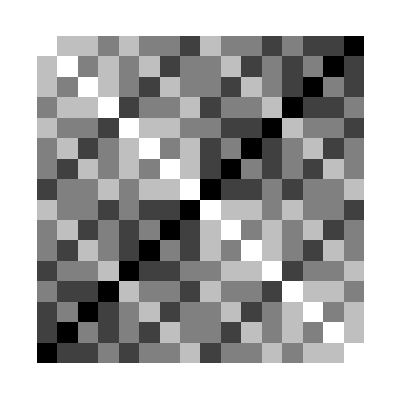

```mathematica
nibbleHammingDistances=Table[HammingDistance[PadLeft[IntegerDigits[i,2],4],PadLeft[IntegerDigits[j,2],4]],{i,0,15},{j,0,15}];
(* nibbleHammingDistances//OutputForm *)
 nibbleHammingDistances//ArrayPlot
```

It’s even more cool with bytes:

```mathematica
byteHammingDistances=Table[HammingDistance[PadLeft[IntegerDigits[i,2],8],PadLeft[IntegerDigits[j,2],8]],{i,0,255},{j,0,255}];
byteHammingDistances//ArrayPlot
```

-Graphics-

## Independent Random Noise

Check the statistical formula at the top of Page 148 of Cogn Comput (2009) 1:139-159 by Kanerva:

```mathematica
Module[{x=rands[],y=rands[],xn,yn,xnoise=0.25,ynoise=1./3,e,f,g},
xn=noisy[x,xnoise];
yn=noisy[y,ynoise];
f=distance[xn,x];
g=distance[yn,y];
e=f+g-2f g;
Print[<|"f+g-2fg"->e,"check"->distance[hmul[xn,yn],hmul[x,y]],
"check2"->distance[hsum[xn,yn],hsum[x,y]],"f"->f,"g"->g|>]]
```

<|f+g-2fg→0.418327,check→0.414795,check2→0.400879,f→0.25293,g→0.334717|>

## Tautologies

```mathematica
implies[a_,b_]:=(¬a∨b);
```

```mathematica
TautologyQ[a⊻(a∧b)⧦(a∧¬b)⧦¬(¬a∨b)⧦¬implies[a,b]]
```

True

```mathematica
TautologyQ[a⊻((¬a)∧b)⧦(a∨b)]
```

True

## Grandmother Example

Modeled from Alex’s original. Show that we can machine-learn that:

A small training set of 15 transitive examples of Proposition U(X,Y,Z): 
	[( X is the mother of Y and Y is the father of Z ) implies ( X is the grandmother of Y )] 
statistically yields — by at least six sigmas — the particular case

Anna is the mother of Bill and Bill is the father of Cid implies that Anna is the grandmother of Cid

### Method

Let G_particular be the proposition Anna is the grandmother of Cid.

Let M be Anna is the mother of Bill. Let F be Bill is the father of Cid. Let H_particular be M and F. Don’t connect H_particular to G_particular, yet.

Let T_random be the conjunction (the and) of several transitivity statements — X is the mother of Y and Y is the father of Z imply X is the grandmother of Z, for randomly selected persons X, Y, and Z.

Test if T_random implies H_particular, then G_particular obtains, statistically at least.

### Algorithm

With implication as bit-vector mul (XOR) and conjunction as bit-vector sum (Majority), Let P be a random permutation, and let g, m, and f be random bit-vectors representing relations. Let A, B, C be random bit-vectors representing the particular persons of interest. Let X_i, Y_i, Z_i for i∈[1..15] be random components of the training examples.

Let G=(P(g)⇒A)∧(P^-1(g)⇒C), the direct example to reproduce statistically.

Let M=(P(m)⇒A)∧(P^-1(m)⇒B) .

Let F=(P(f)⇒B )∧(P^-1(f)⇒C).

Let H=M∧F, transitive statement to include in the final implication T⇒H.

Let M_i=(P(m)⇒X_i )∧(P^-1(m)⇒Y_i), component of training.

Let F_i=(P(f)⇒Y_i )∧(P^-1(f)⇒Z_i), component of training.

Let G_i=(P(g)⇒X_i )∧(P^-1(g)⇒Z_i), component of training.

Let T=∧_(i=1)^15(M_i∧F_i⇒G_i) be the conjunction of the 15 training examples of Proposition U.

Let G'=(T⇒H ).

Show G≈G', statistically.

### Paradox

Hmul is impliedBy, but hmul is symmetric and impliedBy is not symmetric!

Re-interpret hmul as equivalent; arrive at the following equations by substituting ⇔ for ⇒ in the mathematical statement:

G=(P(g)⇔A)∧(P^-1(g)⇔C)

M=(P(m)⇔A)∧(P^-1(m)⇔B)

F=(P(f)⇔B )∧(P^-1(f)⇔C)

H=M∧F

M_i=(P(m)⇔X_i )∧(P^-1(m)⇔Y_i)

F_i=(P(f)⇔Y_i )∧(P^-1(f)⇔Z_i)

G_i=(P(g)⇔X_i )∧(P^-1(g)⇔Z_i)

T=∧_(i=1)^15(M_i∧F_i⇔G_i)

G'=(T⇔H )

G≈G'

These equations imply the equations in the algorithm, so the interpretation of hmul as impliedBy is sound.

<|hamming→3678,stds apart→-9.23658,related?→True,unrelated?→False|>

<|hamming→3724,stds apart→-8.22012,related?→True,unrelated?→False|>

<|hamming→3773,stds apart→-7.13736,related?→True,unrelated?→False|>

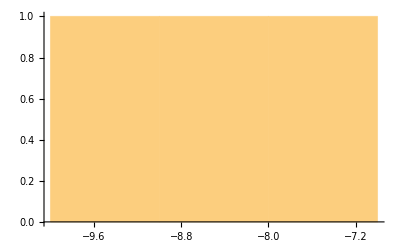

```mathematica
ClearAll[relOf,example,grandmother];
With[{d=8192,impliedBy=hmul,and=hsum},
relOf[p_?PermutationCyclesQ,rel_,x_,y_]:=
Module[{ip,xIsARelOfSomeone,yIsThatSomeoneByInverseRel},
ip=InversePermutation[p];
xIsARelOfSomeone=impliedBy[permute[rel,p],x];
yIsThatSomeoneByInverseRel=impliedBy[permute[rel,ip],y]; 
and[xIsARelOfSomeone,yIsThatSomeoneByInverseRel]];
example[p_?PermutationCyclesQ,motherOf_,fatherOf_,grandmotherOf_]:=
Module[{a=rands[d],b=rands[d],c=rands[d],
aIsMotherOfB,bIsFatherOfC,aIsGrandmotherOfC,
aIsMotherOfBAndBIsFatherOfC},
aIsMotherOfB=relOf[p,motherOf,a,b];
bIsFatherOfC=relOf[p,fatherOf,b,c];
aIsGrandmotherOfC=relOf[p,grandmotherOf,a,c];
aIsMotherOfBAndBIsFatherOfC=and[aIsMotherOfB,bIsFatherOfC];
impliedBy[aIsGrandmotherOfC,aIsMotherOfBAndBIsFatherOfC]];
grandmother[NSAMPLES_:15]:=
Module[{rel,motherOf,fatherOf,grandmotherOf,
examples,trained,anna,bill,cid,amb,bfc,abc,agc,agc2},
rel=RandomPermutation[d];
motherOf=rands[d];fatherOf=rands[d];grandmotherOf=rands[d];
anna=rands[d];bill=rands[d];cid=rands[d];
(* assert Anna grandmotherOf Cid directly *)
agc=relOf[rel,grandmotherOf,anna,cid];
(* train several transitive examples *);
examples=Table[example[rel,motherOf,fatherOf,grandmotherOf],{i,NSAMPLES}];
trained=and@@examples;
(* check whether training implies Anna gm of Cid *);
amb=relOf[rel,motherOf,anna,bill];
bfc=relOf[rel,fatherOf,bill,cid];
abc=and[amb,bfc];
agc2=impliedBy[abc,trained];
Print@<|"hamming"->hamming[agc,agc2],
"stds apart"->stdApart[agc,agc2],
"related?"->related[agc,agc2],
"unrelated?"->unrelated[agc,agc2]|>;
stdApart[agc,agc2]]//AbsoluteTiming];
Histogram[#[[2]]&/@Table[grandmother[15],{i,3}]]
```

In two runs, there were 5/100 cases where “related” passed a 5-sigma test, but not a 6-sigma test.

# Permutation Encoding

We must specify permutations of 8-Kibi BHVs and encode such permutations, themselves, in 8-Kibi BHVs.

## Bitwise

```mathematica
Module[{r=RandomPermutation[8192]},
{Length[r],Length/@r}]
```

{1,Cycles[10]}

## Bytewise

## Deficient Bytewise

The minimum number of bits needed to represent every

```mathematica
Log[2,1024!]//N
```

8769.01

```mathematica
Log[2,8192!]//N
```

94685.3

```mathematica
8192Log[2,8192]/8192
```

13

```mathematica
512Log[2,512]
```

4608

```mathematica
ResourceFunction["HuffmanEncode"]
```

```mathematica
ResourceFunction[""]
```

# Hamming on APU

## Resonators, Comb

Each row in the upcoming combs matrix is a resonator for its 0-based row index. Row 0 resonates with 0, row 6 resonates with 6, etc . A resonator is a sequence of four bits across plats (horizontally) in a section, not four bits across sections (vertically).

Materialize combs  in-section, that is, each row of combs inhabits section 0 of a different VR. The matrix below is “looking down” on the cuboid from behind at only the top section, section 0, with contents in hex. Must have 16 VRs for the combs matrix.

An input will leave F only in the row where a nibble equals the resonator in the row. For instance, an 8 in the third column of the input

{4, C, 8, A, D, C, C, ..., 4, D, 7}

“resonates” with the row full of 8’s, leaving an F in that row and in only that row. 8 will not fully “resonate” with any other row and will not leave F in any other row, though it will leave some bits on.

```mathematica
hammingDemoDim=128;bitsPerNibble=4;
```

```mathematica
MatrixForm[asHex/@(combs=Table[
fromHex[ConstantArray[c,hammingDemoDim/bitsPerNibble]],
{c,Characters["0123456789ABCDEF"]}])]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9
A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A | A
B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B | B
C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C
D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D | D
E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E | E
F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F)

## Nock

Nock is named after the slot for the bow-string in an arrow shaft.

Nock is a Boolean function that turns all bits off in a nibble if any bit is off, that is, turns anything but F into zero, and F into some arbitrary non-zero. Here, 8 stands for F for momentary convenience:

```mathematica
Module[{t=rands[hammingDemoDim],combed,nocked},
prhex@t;
combed=Map[comb[t,#]&,combs];
nocked=nock/@combed;
Print[ReplaceAll[asHex/@nocked,{0->"."}]//MatrixForm];]
```

(E | C | 5 | 5 | 6 | 6 | B | 1 | 8 | 2 | 1 | C | 5 | 3 | A | D | 2 | 2 | D | B | 3 | 9 | 0 | 5 | 5 | 5 | E | B | 0 | E | D | F)

(. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | 8 | . | . | .
. | . | . | . | . | . | . | 8 | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | 8 | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | 8 | 8 | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | 8 | 8 | 8 | . | . | . | . | . | .
. | . | . | . | 8 | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | 8 | . | . | . | .
. | 8 | . | . | . | . | . | . | . | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | 8 | . | . | . | . | . | . | . | . | . | . | . | 8 | .
8 | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 | . | . | 8 | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8)

Nock leaves an 8 in the resonating row.

With two input vectors, count the number of bits different in the two. A vector containing the differing bits between vectors a and b is Not[BitXor[a, b].

With each of the sixteen rows in combs goes a bit-count. The bit counts inhabit sections 1, 2, 3 of each VR because the bit-counts vary from 0 to 4, requiring 3 bits. It’s easiest to load the bit counts as constants. The inner product of each column of nocked with the bit counts produces a vector with 8 times the number of ON bit in the original input:

```mathematica
bitsOn={0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4}
```

{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4}

```mathematica
Module[{t=rands[hammingDemoDim],combed,sumbo,nocked,
numnocked},
prhex@t;
combed=Map[comb[t,#]&,combs];
nocked=nock/@combed;
numnocked=asHex/@nocked;
(*Print[MatrixForm@numnocked];*);
sumbo={bitsOn.numnocked/8};
Print[MatrixForm@sumbo];
]
```

(8 | 0 | B | B | B | 9 | 9 | 3 | E | 3 | E | 6 | 2 | 2 | 7 | 7 | 2 | 2 | D | E | F | F | 0 | B | 9 | B | 7 | B | 7 | B | F | 8)

(1 | 0 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 2 | 1 | 1 | 3 | 3 | 1 | 1 | 3 | 3 | 4 | 4 | 0 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 4 | 1)

## Warren’s Way (UNDONE)

I found a tree-wise method of summing up the bit counts on the APU, reducing the sums from 32K to a max of 512+256+128+64+32+16+12+8+4 = 1032, with 12 clocks for each add, so 1032*12 = 12384 clocks. The number of adds in the APU is tunable.

### Henry S. Warren, Jr, “Hacker’s Delight,” 2d Ed., p 81 ff.

-Graphics-

Start with a “word-length” of 128 bits.

```mathematica
asHex@(a128sample=rands[128])
```

{9,B,F,1,C,6,1,C,8,E,8,5,6,8,D,9,0,D,B,C,D,A,A,E,D,0,6,E,3,9,9,F}

```mathematica
asInt@a128sample
```

207285701069167080847398672473481165215

```mathematica
(nibbleMask1=fromHex[ConstantArray["5",hammingDemoDim/bitsPerNibble]])//asHex
asInt@nibbleMask1
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

113427455640312821154458202477256070485

```mathematica
x11=BitAnd[asInt@a128sample,asInt@nibbleMask1]
x12=BitAnd[BitShiftRight[asInt@a128sample,1],asInt@nibbleMask1]
x1=x11+x12
asBin@fromDimInt[128,x1]
```

23018832763545477870541903009119736085

92133434152810801488428384732180714565

115152266916356279358970287741300450650

{0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,1,1,0,1,0,0,0,1,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0}

```mathematica
(nibbleMask2=fromHex[ConstantArray["3",128/4]])//asHex
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
x211=BitAnd[x1,asInt@nibbleMask2]
x212=BitAnd[BitShiftRight[x1,2],asInt@nibbleMask2]
x2=x211+x212
```

24097471270831108711090277331424583954

22763698911381292661970002602468966674

46861170182212401373060279933893550628

```mathematica
(nibbleMask3=fromHex[Riffle[ConstantArray["0",128/2/4],ConstantArray["F",128/2/4]]])//asHex
```

{0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F,0,F}

```mathematica
x321=BitAnd[x2,asInt@nibbleMask3]
x322=BitAnd[BitShiftRight[x2,4],asInt@nibbleMask3]
x3=x321+x322
```

3992917008419692418789448184324358660

2679265823362044309641926984348074498

6672182831781736728431375168672433158

```mathematica
(nibbleMask4=fromHex@Flatten[ConstantArray[Characters["00FF"],128/4/4]])//asHex
```

{0,0,F,F,0,0,F,F,0,0,F,F,0,0,F,F,0,0,F,F,0,0,F,F,0,0,F,F,0,0,F,F}

```mathematica
x431=BitAnd[x3,asInt@nibbleMask4]
x432=BitAnd[BitShiftRight[x3,8],asInt@nibbleMask4]
x4=x431+x432
```

25961721980788550629636914708545542

25961801210159953819538040054546436

51923523190948504449174954763091978

```mathematica
(nibbleMask5=fromHex@Flatten[ConstantArray[Characters["0000FFFF"],128/8/4]])//asHex
```

{0,0,0,0,F,F,F,F,0,0,0,0,F,F,F,F,0,0,0,0,F,F,F,F,0,0,0,0,F,F,F,F}

```mathematica
x541=BitAnd[x4,asInt@nibbleMask5]
x542=BitAnd[BitShiftRight[x4,16],asInt@nibbleMask5]
x5=x541+x542
```

554597137747424315787433738250

792281625271770584485766103048

1346878763019194900273199841298

```mathematica
(nibbleMask6=fromHex@Flatten[ConstantArray[Characters["00000000FFFFFFFF"],128/16/4]])//asHex
```

{0,0,0,0,0,0,0,0,F,F,F,F,F,F,F,F,0,0,0,0,0,0,0,0,F,F,F,F,F,F,F,F}

```mathematica
x651=BitAnd[x5,asInt@nibbleMask6]
x652=BitAnd[BitShiftRight[x5,32],asInt@nibbleMask6]
x6=x651+x652
asBin[fromDimInt[128,x6]]
```

276701161105643274258

313594649253062377490

590295810358705651748

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0}

```mathematica
(nibbleMask7=fromHex@Flatten[ConstantArray[Characters["0000000000000000FFFFFFFFFFFFFFFF"],128/32/4]])//asHex
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F}

```mathematica
x761=BitAnd[x6,asInt@nibbleMask7]
x762=BitAnd[BitShiftRight[x6,64],asInt@nibbleMask7]
x7=x761+x762
```

36

32

68

Now check against the prior method:

```mathematica
Module[{t=a128sample,combed,sumbo,nocked,
numnocked},
prhex@t;
combed=Map[comb[t,#]&,combs];
nocked=nock/@combed;
numnocked=asHex/@nocked;
(*Print[MatrixForm@numnocked];*);
sumbo={bitsOn.numnocked/8};
Print[MatrixForm@sumbo];
Apply[Plus,sumbo[[1]]]
]
```

(9 | B | F | 1 | C | 6 | 1 | C | 8 | E | 8 | 5 | 6 | 8 | D | 9 | 0 | D | B | C | D | A | A | E | D | 0 | 6 | E | 3 | 9 | 9 | F)

(2 | 3 | 4 | 1 | 2 | 2 | 1 | 2 | 1 | 3 | 1 | 2 | 2 | 1 | 3 | 2 | 0 | 3 | 3 | 2 | 3 | 2 | 2 | 3 | 3 | 0 | 2 | 3 | 2 | 2 | 2 | 4)

68

To perform this on the APU, we need a section-wise add over 2048-bit words.

```mathematica
(a40=rands[40])//asBin
(b40=rands[40])//asBin
```

{0,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,1,0}

{0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,0,1,0,0,1,1,1,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0}

sum bits:

```mathematica
xor[a40,b40]//asBin
```

{0,0,0,1,1,1,0,0,1,0,0,1,1,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0}

carry bits:

```mathematica
and[a40,b40]//asBin
```

{0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

```mathematica
erl[and[a40,b40]]//asBin
```

{0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}

# One-Bit Mandelbrot (UNDONE)

Number cells in the upper-left, 256×256 corner of the MMB as follows:

```mathematica
ClearAll[hb,nVR,nPlat,nSect];
nVR=16;nSect=16;nPlat=nVR*nSect; 
hb=ConstantArray[0,{nVR,nPlat,nSect}]
```

Map this to a 2D array by letting the first index be

```mathematica
hb[[Sequence[1,2,3]]]
```

0

```mathematica
ClearAll[twoDGraphicsConventionToVPS];
twoDGraphicsConventionToVPS[i_,j_]:=Sequence[1+Quotient[i,nSect],1+j,1+Mod[i,nSect]];
hb[[twoDGraphicsConventionToVPS[1,2]]]
(**)
```

0

```mathematica
ArrayPlot[Table[hb[[twoDGraphicsConventionToVPS[i,j]]],{i,0,255},{j,0,255}]]
```

-Graphics-

```mathematica
ClearAll[twoDGraphicsConventionToComplexPlane,lirp];
lirp[x_,nx_,xx_,ny_,xy_]:=N[ny+x(xy-ny)/(xx-nx)];
twoDGraphicsConventionToComplexPlane[i_,j_]:=Module[{
minI=0,maxI=255,minJ=0,maxJ=255,
minCX=-2.,maxCX=1.0,minCY=-1.5,maxCY=1.5},
Complex[lirp[j,minJ,maxJ,minCX,maxCX],lirp[i,minI,maxI,minCY,maxCY]]];
twoDGraphicsConventionToComplexPlane[127,0]
```

-2.-0.00588235 ⅈ

```mathematica
ClearAll[mandIterate,mandIter];
mandIterate[z_,c_]:=N[z^2]+c;
mandIter[f_,c_,iter_,maxIter_]:=
((*Print[<|"f"->f,"|f|"->Abs[f],"c"->c,"i"->iter,"m"->maxIter|>];*)
If[iter>=maxIter,
1,(*else*)
If[Abs[f]>2.0,
0,(*else*)
mandIter[mandIterate[f,c],c,iter+1,maxIter]]]);
```

```mathematica
ArrayPlot[Table[mandIter[
(*z*)Complex[0.,0.],
(*c*)twoDGraphicsConventionToComplexPlane[i,j],
0,100],
{i,0,255,1},
{j,0,255,1}]]
```

-Graphics-

# Programming Modes

```mathematica
ClearAll[cStyle];
leptonStyle[xs_]:=Style[Labeled[xs,"Lepton\nARC+MMB\nAlpha"],LightBrown];
leptonMmbStyle[xs_]:=Style[Labeled[xs,""],LightBrown];
pythonStyle[xs_]:=Style[Labeled[xs,"Python\nHost+ARC\nProd"],LightGreen];
lpythonStyle[xs_]:=Style[Labeled[xs,"LPython\nHost+ARC\nAlpha"],LightRed];
baryonStyle[xs_]:=Style[Labeled[xs,"Baryon\nARC+MMB\nAlpha"],LightBlue];
cHostStyle[xs_]:=Style[Labeled[xs,"C\nHost\nProd"],LightGray];
cArcStyle[xs_]:=Style[Labeled[xs,"C\nARC\nProd"],LightGray];
cHostArcStyle[xs_]:=Style[Labeled[xs,"C\nHost+ARC\nProd"],LightGray];
diriStyle[xs_]:=Style[Labeled[xs,"Diri\nnanosim\n+compiled\nProd"],LightYellow];
belexStyle[xs_]:=Style[Labeled[xs,"Belex\nMMB\nProd"],Yellow];
compiledStyle[xs_]:=Style[Labeled[xs,"Compiled"],White];
pecosStyle[xs_]:=Style[Labeled[xs,"\"Pecos\"\nCopperhead\nProd"],Lighter[LightGray]];
mocassinStyle[xs_]:=Style[Labeled[xs,"\"Moccasin\"\nCopperhead\nAlpha/Prod"],LightMagenta];
mocassinProdStyle[xs_]:=Style[Labeled[xs,"\"Moccasin\"\nCopperhead\nProd"],LightMagenta];
mocassinAlphaStyle[xs_]:=Style[Labeled[xs,"\"Moccasin\"\nCopperhead\nAlpha"],LightMagenta];
unnamedStyle[xs_]:=Style[Labeled[xs,"? unnamed ?"],White];
contortedStyle[xs_]:=Style[Labeled[xs,"\"Contorted\"\nCopperhead\nAlpha"],LightCyan];
SectorChart[{
{belexStyle[{9,1}],leptonMmbStyle[{3,1}]},
{cArcStyle[{3,1}],diriStyle[{3,1}],baryonStyle[{3,1}],leptonStyle[{3,1}]},
{cHostStyle[{3,1}],pythonStyle[{1.5,1}],lpythonStyle[{1.5,1}],cHostArcStyle[{1,1}],lpythonStyle[{1,1}],pythonStyle[{1,1}],pythonStyle[{1,1}],lpythonStyle[{1,1}],cHostArcStyle[{1,1}]},
{pecosStyle[{3,1}],mocassinProdStyle[{1.5,1}],mocassinAlphaStyle[{1.5,1}],contortedStyle[{6,1}]}
},
(*ChartLabels->{"a","b","c","d","e","f","g","h","i"},*)
(*ChartStyle->ColorData[3,"ColorList"],*)
SectorOrigin->3Pi/2,SectorSpacing->0,ImageSize->Large]
```

-Graphics-

```mathematica
{{, "full emu", "lepton", "baryon", "mixed-mode", "hardware"}, {"matvec", ✓, ✓, ✓, ✓, ✓}, {"belex-direct-fragment", ✓, , ✓, ✓, ✓}, {"lcg", , ✓, ✓, , ✓}, {"matmul", ✓, ✓, ✓, , ✓}, {"matmul w/o parity", , , ✓, , ✓}, {"belex tests", ✓, , ✓, , ✓}, {"game of life", , , ✓, , ✓}, {"custom belex", ✓, , ✓, , ✓}}
```

{{Null,full emu,lepton,baryon,mixed-mode,hardware},{matvec,✓,✓,✓,✓,✓},{belex-direct-fragment,✓,Null,✓,✓,✓},{lcg,Null,✓,✓,Null,✓},{matmul,✓,✓,✓,Null,✓},{matmul w/o parity,Null,Null,✓,Null,✓},{belex tests,✓,Null,✓,Null,✓},{game of life,Null,Null,✓,Null,✓},{custom belex,✓,Null,✓,Null,✓}}

```mathematica
{{, "leptonic Python", "baryonic Python"}, {"matvec", ✓, }, {"belex-direct-fragment", , ✓}, {"lcg", , }, {"matmul", ✓, }, {"matmul w/o parity", , }, {"game of life", , }, {"custom belex", , ✓}}
```

{{Null,leptonic Python,baryonic Python},{matvec,✓,Null},{belex-direct-fragment,Null,✓},{lcg,Null,Null},{matmul,✓,Null},{matmul w/o parity,Null,Null},{game of life,Null,Null},{custom belex,Null,✓}}

```mathematica
leptonStyle3D[xs_]:=Style[Labeled[Append[10]@xs,Lepton],Orange];
pythonStyle3D[xs_]:=Style[Labeled[Append[4]@xs,Python],Yellow];
lpythonStyle3D[xs_]:=Style[Labeled[Append[6]@xs,LPython],Magenta];
baryonStyle3D[xs_]:=Style[Labeled[Append[10]@xs,Baryon],RGBColor[.8,.6,1.0]];
cStyle3D[xs_]:=Style[Labeled[Append[8]@xs,C],Cyan];
diriStyle3D[xs_]:=Style[Labeled[Append[10]@xs,Diri],Yellow];
belexStyle3D[xs_]:=Style[Labeled[Append[12]@xs,Belex],Yellow];
compiledStyle3D[xs_]:=Style[Labeled[Append[8]@xs,Compiled],White];
pecosStyle3D[xs_]:=Style[Labeled[Append[2]@xs,"\"Pecos\"\nCopperhead"],Violet];
mocassinStyle3D[xs_]:=Style[Labeled[Append[2]@xs,"\"Moccasin\"\nCopperhead"],Pink];
unnamedStyle3D[xs_]:=Style[Labeled[Append[2]@xs,"? unnamed ?"],White];
contortedStyle3D[xs_]:=Style[Labeled[Append[2]@xs,"\"Contorted\"\nCopperhead"],Green];
SectorChart3D[{
{belexStyle3D[{9,1}],leptonStyle3D[{3,1}]},
{cStyle3D[{3,1}],compiledStyle3D[{1,1}],diriStyle3D[{1,1}],compiledStyle3D[{1,1}],baryonStyle3D[{3,1}],leptonStyle3D[{3,1}]},
{cStyle3D[{3,1}],pythonStyle3D[{1.5,1}],lpythonStyle3D[{1.5,1}],cStyle3D[{1,1}],lpythonStyle3D[{1,1}],pythonStyle3D[{1,1}],pythonStyle3D[{1,1}],lpythonStyle3D[{1,1}],cStyle3D[{1,1}]},
{pecosStyle3D[{3,1}],mocassinStyle3D[{3,1}](*,unnamedStyle3D[{1,1}]*),contortedStyle3D[{6,1}](*,unnamedStyle3D[{1,1}]*)}
},SectorOrigin->3Pi/2,SectorSpacing->0,ImageSize->Large]
```

-Graphics3D-